# 3. izpit – Mathematica

## Računalniški praktikum 2024/25

Študijska smer : Matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

V tem delu izpita sta dve nalogi, ki sta skupaj vredni 32 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.

## 1. naloga [12 točk]

1. (4 točke) Izračunajte vsoto ∑_(k=1)^30 k^2/(k+5).
2. (4 točke) Rešite neenačbo:|x-1|≤ 2x+3 
3. (4 točke) Izračunajte drugi odvod funkcije  3tg (2cos(x)+1)  sin (x) in ga poenostavite.

```mathematica
Sum[k^2/(k+5),{k,1,30}]
Reduce[Abs[x-1]<=2x+3]
Simplify[D[3 Tan[2 Cos[x]+1] Sin[x],{x,2}]]
```

189870299151349/525103828704

x≥-2/3

-3 Sin[x] (6 Cos[x] Sec[1+2 Cos[x]]^2+(1-8 Sec[1+2 Cos[x]]^2 Sin[x]^2) Tan[1+2 Cos[x]])

## 2. naloga [20 točk]

1. (5 točk) Definirajte funkciji x(t)=cos(5t) in y(t)=0.5 sin(t).
2. (5 točk) Poiščite take vrednosti t ∈ [0, π], da velja x(t)=0
3. (5 točk) Narišite parametrično podano krivuljo na območju t ∈[0,2π].
4. (5 točk) Z ukazom Manipulate predstavite, kako se spreminja krivulja, 
če funkcijo x(t) zamenjamo s cos(a t), kjer a teče po celih številih med 1 in 7.

{{t→π/10},{t→(3 π)/10},{t→π/2},{t→(7 π)/10},{t→(9 π)/10}}

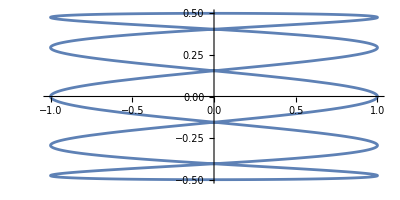

```mathematica
x[t_]:=Cos[5t]
y[t_]:=0.5Sin[t]
Solve[x[t]==0&&t>=0&&t<=Pi,t]
ParametricPlot[{x[t],y[t]},{t,0,2Pi}]
Manipulate[
ParametricPlot[{Cos[a t],y[t]},{t,0,2Pi}],
{a,1,7}
]
```